```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/17/2010     *)

(*Assignment #3
Problem #2     *)
```

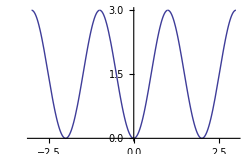

```mathematica
L=1;
fbas[x_]:=7x^2-5x^4+x^6;
f[x_]:=fbas[Mod[x,2×L,-L]];
Plot[f[x],{x,-3,3}]
```

```mathematica
(*  Since there are no discontinuities in the finction nor any of its derivatives, I predict that the coefficients will drop off with a high power of n in the denominator (specifically n approxamately on the order of the highest power od x in the function x^6).   *)
```

```mathematica
(* Problem #2*)
```

```mathematica
aF[0]=1/(2 L)∫_-L^L f[x]ⅆx
```

31/21

```mathematica
aF[n_]=Simplify[1/L∫_-L^L f[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

(1440 (-1)^n)/(n^6 π^6)

```mathematica
bF[n_]=Simplify[1/L∫_-L^L f[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
coeffsF=Table[{aF[i],bF[i]},{i,1,20}];
TableForm[coeffsF]
```

-1440/π^6 | 0
45/(2 π^6) | 0
-160/(81 π^6) | 0
45/(128 π^6) | 0
-288/(3125 π^6) | 0
5/(162 π^6) | 0
-1440/(117649 π^6) | 0
45/(8192 π^6) | 0
-160/(59049 π^6) | 0
9/(6250 π^6) | 0
-1440/(1771561 π^6) | 0
5/(10368 π^6) | 0
-1440/(4826809 π^6) | 0
45/(235298 π^6) | 0
-32/(253125 π^6) | 0
45/(524288 π^6) | 0
-1440/(24137569 π^6) | 0
5/(118098 π^6) | 0
-1440/(47045881 π^6) | 0
9/(400000 π^6) | 0

```mathematica
Fs[k_,x_]:=coeffsG[[k,1]]*Cos[k*Pi*x/L]+coeffsG[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourierF[n_,x_]:=aF[0]+∑_(k=1)^n Fs[k,x]
```

```mathematica
fourierF[5,x]
```

31/21+(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)

```mathematica
N[fourierF[5,x],1]
```

1.+5. Sin[3. x]-0.1 Sin[6. x]+0.02 Sin[9. x]-0.005 Sin[10. x]+0.002 Sin[20. x]

```mathematica
fourierF[10,x]
```

31/21+(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)-(5 Sin[6 π x])/(27 π^5)+(1440 Sin[7 π x])/(16807 π^5)-(45 Sin[8 π x])/(1024 π^5)+(160 Sin[9 π x])/(6561 π^5)-(9 Sin[10 π x])/(625 π^5)

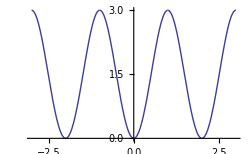

```mathematica
graphoneF=Plot[f[x],{x,-3,3},Exclusions->{-1,1}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

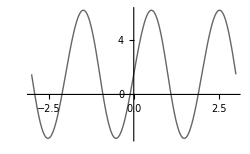

```mathematica
graphtwoF=Plot[fourierF[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

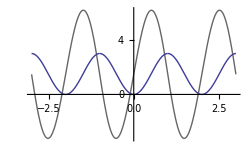

```mathematica
bothtwoF=Show[graphtwoF,graphoneF]
```

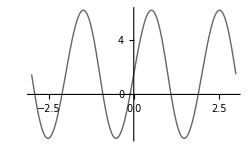

```mathematica
graphthreeF=Plot[fourierF[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

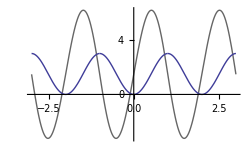

```mathematica
boththreeF=Show[graphthreeF,graphoneF]
```

```mathematica
graphsixF=Plot[fourierF[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

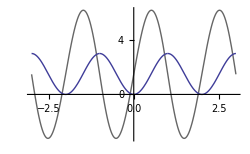

```mathematica
bothsixF=Show[graphsixF,graphoneF]
```

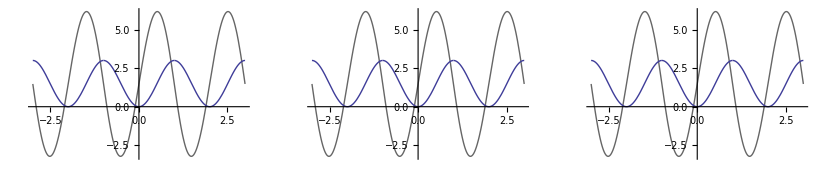

```mathematica
Show[GraphicsRow[{bothtwoF,boththreeF,bothsixF}]]
```

```mathematica
(*taking the derivative of the original base function*)
```

```mathematica
D[fbas[x],x]
```

14 x-20 x^3+6 x^5

```mathematica
(*Taking the derivative of the fourier approximation of fbas      *)
D[fourierF[5,x],x]
```

(1440 Cos[π x])/π^4-(90 Cos[2 π x])/π^4+(160 Cos[3 π x])/(9 π^4)-(45 Cos[4 π x])/(8 π^4)+(288 Cos[5 π x])/(125 π^4)

```mathematica
(* Now I will create the Fourier Series for approximating g(x)    *)
```

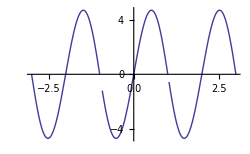

```mathematica
L=1;
gbas[x_]:=14x-20x^3+6x^5
g[x_]:=gbas[Mod[x,2×L,-L]];
Plot[g[x],{x,-3,3}]
```

```mathematica
(*  Since there are no discontinuities in the finction nor any of its derivatives, I predict that the coefficients will drop off with a high power of n in the denominator (specifically n approxamately on the order of the highest power od x in the function x^6).   *)
```

```mathematica
(* Problem #2*)
```

```mathematica
aG[0]=1/(2 L)∫_-L^L g[x]ⅆx
```

0

```mathematica
aG[n_]=Simplify[1/L∫_-L^L g[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
bG[n_]=Simplify[1/L∫_-L^L g[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

-(1440 (-1)^n)/(n^5 π^5)

```mathematica
∫_-L^L (fourierG[10,x])^2ⅆx
```

413520574906423083987893722912609/(199223430891250139136000000 π^10)

```mathematica
(2L(aG[0])^2+L∑_(n=1)^∞ (aG[n])^2+(bG[n])^2)
```

(2073600 (-1)^(2 n))/(n^10 π^10)

```mathematica
coeffsG=Table[{aG[i],bG[i]},{i,1,20}];
TableForm[coeffsG]
```

0 | 1440/π^5
0 | -45/π^5
0 | 160/(27 π^5)
0 | -45/(32 π^5)
0 | 288/(625 π^5)
0 | -5/(27 π^5)
0 | 1440/(16807 π^5)
0 | -45/(1024 π^5)
0 | 160/(6561 π^5)
0 | -9/(625 π^5)
0 | 1440/(161051 π^5)
0 | -5/(864 π^5)
0 | 1440/(371293 π^5)
0 | -45/(16807 π^5)
0 | 32/(16875 π^5)
0 | -45/(32768 π^5)
0 | 1440/(1419857 π^5)
0 | -5/(6561 π^5)
0 | 1440/(2476099 π^5)
0 | -9/(20000 π^5)

```mathematica
Gs[k_,x_]:=coeffsG[[k,1]]*Cos[k*Pi*x/L]+coeffsG[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourierG[n_,x_]:=aG[0]+∑_(k=1)^n Gs[k,x]
```

```mathematica
fourierG[5,x]
```

(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)

```mathematica
(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)
```

(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)

```mathematica
N[fourierG[5,x],1]
```

5. Sin[3. x]-0.1 Sin[6. x]+0.02 Sin[9. x]-0.005 Sin[10. x]+0.002 Sin[20. x]

```mathematica
fourierG[10,x]
```

(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)-(5 Sin[6 π x])/(27 π^5)+(1440 Sin[7 π x])/(16807 π^5)-(45 Sin[8 π x])/(1024 π^5)+(160 Sin[9 π x])/(6561 π^5)-(9 Sin[10 π x])/(625 π^5)

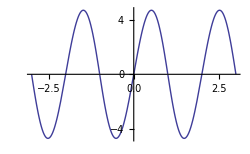

```mathematica
graphoneG=Plot[g[x],{x,-3,3},Exclusions->{-1,1}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

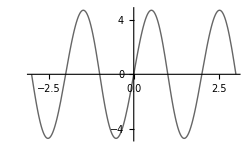

```mathematica
graphtwoG=Plot[fourierG[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

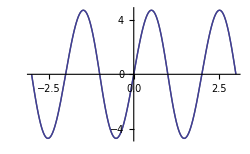

```mathematica
bothtwoG=Show[graphtwoG,graphoneG]
```

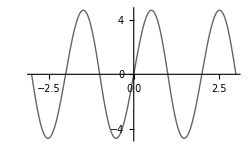

```mathematica
graphthreeG=Plot[fourierG[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

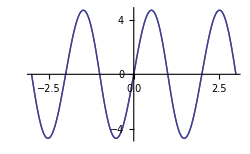

```mathematica
boththreeG=Show[graphthreeG,graphoneG]
```

```mathematica
graphsixG=Plot[fourierG[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

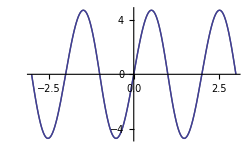

```mathematica
bothsixG=Show[graphsixG,graphoneG]
```

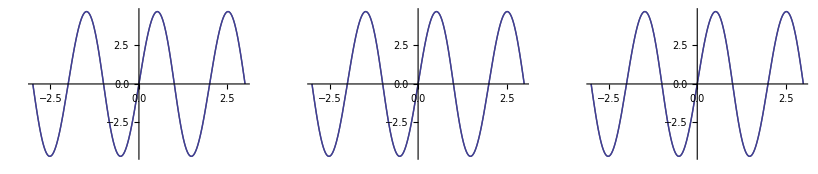

```mathematica
Show[GraphicsRow[{bothtwoG,boththreeG,bothsixG}]]
```

```mathematica
(*taking the derivative of the original base function*)
```

```mathematica
(*Now I will determine if the two functions are related by differentiation*)
```

```mathematica
If[D[fourierF[5,x],x]==fourierG[5,x],"True","False"]
```

If[(1440 Cos[π x])/π^4-(90 Cos[2 π x])/π^4+(160 Cos[3 π x])/(9 π^4)-(45 Cos[4 π x])/(8 π^4)+(288 Cos[5 π x])/(125 π^4)==(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5),True,False]

```mathematica
If[D[fourierF[15,x],x]==fourierG[15,x],"True","False"]
```

If[(1440 Cos[π x])/π^4-(90 Cos[2 π x])/π^4+(160 Cos[3 π x])/(9 π^4)-(45 Cos[4 π x])/(8 π^4)+(288 Cos[5 π x])/(125 π^4)-(10 Cos[6 π x])/(9 π^4)+(1440 Cos[7 π x])/(2401 π^4)-(45 Cos[8 π x])/(128 π^4)+(160 Cos[9 π x])/(729 π^4)-(18 Cos[10 π x])/(125 π^4)+(1440 Cos[11 π x])/(14641 π^4)-(5 Cos[12 π x])/(72 π^4)+(1440 Cos[13 π x])/(28561 π^4)-(90 Cos[14 π x])/(2401 π^4)+(32 Cos[15 π x])/(1125 π^4)==(1440 Sin[π x])/π^5-(45 Sin[2 π x])/π^5+(160 Sin[3 π x])/(27 π^5)-(45 Sin[4 π x])/(32 π^5)+(288 Sin[5 π x])/(625 π^5)-(5 Sin[6 π x])/(27 π^5)+(1440 Sin[7 π x])/(16807 π^5)-(45 Sin[8 π x])/(1024 π^5)+(160 Sin[9 π x])/(6561 π^5)-(9 Sin[10 π x])/(625 π^5)+(1440 Sin[11 π x])/(161051 π^5)-(5 Sin[12 π x])/(864 π^5)+(1440 Sin[13 π x])/(371293 π^5)-(45 Sin[14 π x])/(16807 π^5)+(32 Sin[15 π x])/(16875 π^5),True,False]

```mathematica
(* The fourier series for F converges to F.  The fourier series for G converges to G.  The derivative for the fourier series of F is equal to the fiurier series for G within the first 5, 15 or n terms.     *)
```

```mathematica
(*  Problem #3   *)
```

```mathematica
Integrate[fourierG[5,x],{x,0,y}]
```

1/(8100000 π^6)(22679683710-623227939 Cos[π y]+50176702 Cos[2 π y]-5418657 Cos[3 π y]+2985984 Cos[4 π y]) Sin[(π y)/2]^2

```mathematica
If[Integrate[fourierG[5,x],{x,0,a}]==fourierF[5,a],"True","False"]
```

False

```mathematica
∑_(n=1)^∞ (-1)^(n+1)/n^6
```

(31 π^6)/30240

```mathematica
(* Problem #4  *)
```

```mathematica
(* Part A  *)
```

```mathematica
w={0,0,0};
t={1,0,0};
u={1,1,0};
V={1,1,1};
a=Dot[w,t]/Dot[t,t]
```

0

```mathematica
b=Dot[w,u]/Dot[u,u]
```

0

```mathematica
c=Dot[w,V]/Dot[V,V]
```

0

```mathematica
(* The only constants that make this true are c1=c2=c3=0, which is a trivial solution.  Therefore there are these vectors are a linearly independent basis set, be definition   *)
```

```mathematica
(* Part B  *)
```

```mathematica
w={3,2,4};
t={1,0,0};
u={1,1,0};
V={1,1,1};
a=Dot[w,t]/Dot[t,t]
```

3

```mathematica
b=Dot[w,u]/Dot[u,u]
```

5/2

```mathematica
c=Dot[w,V]/Dot[V,V]
```

3

```mathematica
(*  a is c1, b is c2, and c is c3 as determined by problem #4b   *)
```

```mathematica
(* Part C *)
```

```mathematica
w={3,2,4};
t={1,-2,0};
u={2,1,1};
V={-2,-1,5};
a=Dot[w,t]/Dot[t,t]
```

-1/5

```mathematica
b=Dot[w,u]/Dot[u,u]
```

2

```mathematica
c=Dot[w,V]/Dot[V,V]
```

2/5

```mathematica
(*  a is c1, b is c2, and c is c3 as determined by problem #4 pard d   *)
```

```mathematica
(* Problem #5   *)
```

```mathematica
∫_-1^1 (14x-20x^3+6x^5)^2ⅆx
```

5120/231

```mathematica
(* The following expression *)
∑_(n=1)^∞ (1/n^5)^2
```

π^10/93555

```mathematica
(5120/231)/1440^2
```

1/93555

```mathematica
(*Part B   *)
N[(93555∑_(n=1)^∞ 1/n^10)^(1/10),11]
```

3.1415926536

```mathematica
(* To determine the number of terms it will take to reach a certain accuracy (in this case the ten-billionth place), we look at the power of n, which tells us the rate of convergence.  n will need to be approxamatly ten or greater to give us an error less than one-ten-billionth.  Therefore, at least ten terms should be summed to get this precision.  *)
```

{{n→-10},{n→10},{n→-10 (-1)^(1/5)},{n→10 (-1)^(1/5)},{n→-10 (-1)^(2/5)},{n→10 (-1)^(2/5)},{n→-10 (-1)^(3/5)},{n→10 (-1)^(3/5)},{n→-10 (-1)^(4/5)},{n→10 (-1)^(4/5)}}

```mathematica
Manipulate[N[(93555∑_(n=1)^L 1/n^10)^(1/10),10],{L,1,100}]
```

```mathematica
(* Part C  *)
```

```mathematica
(93555∑_(n=1)^∞ 1/n^10)^(1/10)
```

π

```mathematica
(*   Challenge Problem *)
```